## Connexion DLL

## DLL

```mathematica
Clear[pathToDll]
```

```mathematica
Needs["NETLink`"];
```

```mathematica
InstallNET[];
```

```mathematica
(*pathToDll="C:\\Users\\Clem\\Documents\\ESGI\\projet_annuel_ibd3a\\C++_lib\\Dll-Machine-Learning\\x64\\Debug\\Dll-Machine-Learning.dll";*)
pathToDll="D:\\git\\projet_annuel_ibd3a\\C++_lib\\Dll-Machine-Learning\\x64\\Debug\\Dll-Machine-Learning.dll";
```

```mathematica
return42ExternFunc=DefineDLLFunction["return42",pathToDll,"int",{}];
```

```mathematica
return42ExternFunc[]
```

42

## Cas de tests

### Simple Lineaire

```mathematica
Clear[a,b,c,positivePoints, negativePoints, f]
```

```mathematica
a = RandomInteger[{-5; 5}];
b= RandomInteger[{-5; 5}];
c= RandomInteger[{-5; 5}];
```

```mathematica
f[x_] := -a/b*x+c/b
```

```mathematica
g[x_]:=a*x^2+b*x+c
```

```mathematica
positivePoints = Table[x= RandomReal[{-5, 5}]; {x, f[x] + RandomReal[{0.5, 2}]}, {i,1, 3}]
```

{{-3.61094,4.44473},{0.819264,0.716594},{3.14202,-1.50941}}

```mathematica
negativePoints = Table[x = RandomReal[{-5, 5}];
{x, f[x]-RandomReal[{0.5, 2 }]}, {i,1,3}]
```

{{-2.10868,0.830762},{4.66032,-6.646},{4.06406,-4.64952}}

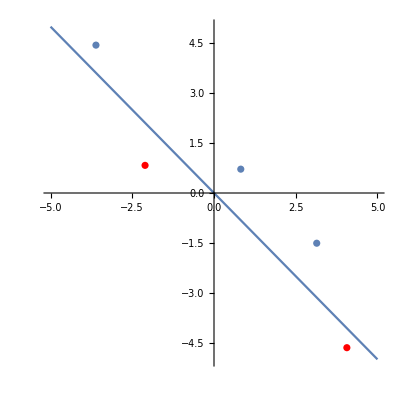

```mathematica
Show[Plot[f[x], g[x], {x,-5, 5}, PlotRange->{-5,5},
AspectRatio->1],
ListPlot[negativePoints, PlotStyle->Red],
ListPlot[positivePoints]]
```

```mathematica
Clear[X, Y, model, createLinearModel, Xtest, Ytest, Xtest2]
```

```mathematica
X = Flatten[{positivePoints, negativePoints}]
```

{-3.61094,4.44473,0.819264,0.716594,3.14202,-1.50941,-2.10868,0.830762,4.66032,-6.646,4.06406,-4.64952}

```mathematica
Y = {1, 1, 1, -1, -1, -1}
```

{1,1,1,-1,-1,-1}

```mathematica
Xtest = {-4.059661874733521,3.88961785568734}
Ytest = {1}
```

{-4.05966,3.88962}

{1}

```mathematica
createLinearModel = DefineDLLFunction["createLinearModel", pathToDll, "System.IntPtr", {"int", "int"}];
```

```mathematica
linearFitClassificationRosenblatt = DefineDLLFunction["linearFitClassificationRosenblatt", pathToDll, "int", {"System.IntPtr", "double[]", "int", "int", "double[]", "int", "int", "double"}];
```

```mathematica
linearClassify =  DefineDLLFunction["linearClassify", pathToDll, "double", {"System.IntPtr", "double[]", "int", "double[]", "int"}];
```

```mathematica
model = createLinearModel[2,1]
```

«NETObject[System.IntPtr]»

```mathematica
linearFitClassificationRosenblatt[model, X, 12, 2, Y, 1, 1000, 0.1];
```

```mathematica
linearClassify[model, Xtest, 2, Ytest, 1]
```

1.

```mathematica
Xtest2 = Partition[Flatten[Table[{i,j},{i, -5, 5, 0.2}, {j, -5, 5, 0.2}]], 2];
```

```mathematica
positive = Select[Xtest2,linearClassify[model, #,2, Ytest,1 ]== 1&];
negative =Select[Xtest2,linearClassify[model, #,2, Ytest,1 ]== -1&];
```

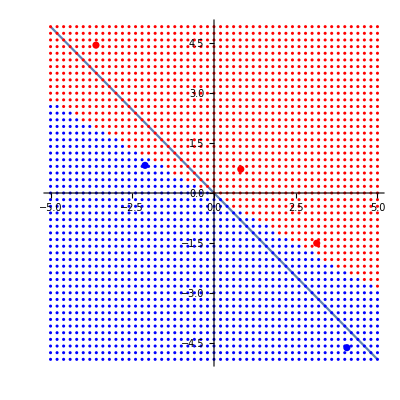

```mathematica
Show[Plot[f[x], {x,-5, 5}, PlotRange->{-5,5},
AspectRatio->1],ListPlot[positive, PlotStyle->Red], ListPlot[negative, PlotStyle->Blue], ListPlot[negativePoints, PlotStyle->Blue, PlotStyle->Thick],
ListPlot[positivePoints, PlotStyle->Red, PlotStyle->Thick]]
```